InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

0

ⅈ √(3/7)

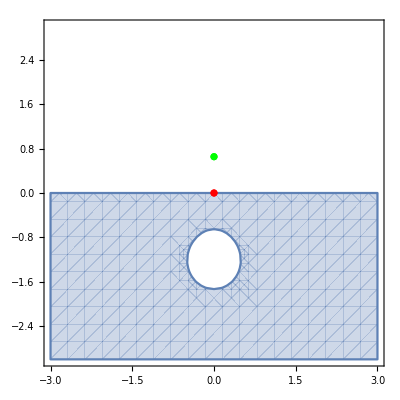

```mathematica
f[n_,t_, z_]:= z/(1-t n z^n)^(1/n)
f[0,t_,z_] := z

region[z_]:=Abs[z] ≤ 1&&Im[z]>0;(*The original region*)h[z_]:= f[0,1,f[2,2/3,f[4,-2/15,z]]];(*The map*)g=InverseFunction[h];(*Its inverse*)
puncture = h[0 + 0I]
midpoint = h[0 + 1I]
Show[RegionPlot[region[g[x+I y]],{x,-3,3},{y,-3,3}, Axes->True], ListPlot[ {{{Re[puncture], Im[puncture]}}, {{Re[midpoint], Im[midpoint]}}}, PlotStyle->{Red, Green}]]
```

```mathematica
RegionPlot[region[g[x+I y]],{x,-3,3},{y,-3,3}, Axes->True]
```

{}